On-shot diagnostic of electron beam-laser pulse interaction based on stochastic quantum radiation reaction

Paper: arXiv: 2007.02841, by Matteo Tamburini
Notebook: Óscar Amaro, August 2021 + January 2023 @ GoLP-EPP

Introduction
Contrary to CRR or MCRR, QRR through stochasticity will induce an asymmetry in the momentum space (x,y) orthogonal to propagation (z), with a visible increase along polarization (x), while in the remaining direction the divergence does not change significantly.

## Figure 2

```mathematica
Clear[m,px,py,σx,σy,p,θ,dNdθ]
n=Exp[-0.5(px^2/σx^2+py^2/σy^2)];
px=p Sin[θ];
py=p Cos[θ];

Integrate[p n,{p,0,∞}]//Normal
```

1/((1. Cos[θ]^2)/σy^2+(1. Sin[θ]^2)/σx^2)

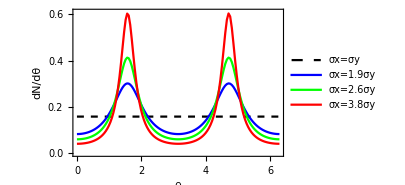

```mathematica
dNdθ[θ_,σx_,σy_]:=1/(Cos[θ]^2/σy^2+Sin[θ]^2/σx^2)
(* approximate choices of σy/σx to match Figure 2 *)
dNdθnorm[θ_,σx_,σy_]:=dNdθ[θ,σx,σy]/NIntegrate[dNdθ[θθ,σx,σy],{θθ,0,2π}]
Plot[{dNdθnorm[θ,1,1],dNdθnorm[θ,1.9,1],dNdθnorm[θ,2.6,1],dNdθnorm[θ,3.8,1]},{θ,0,2π},AxesLabel->{"θ","dN/dθ"},ImageSize->300,PlotLegends->{"σx=σy","σx=1.9σy","σx=2.6σy","σx=3.8σy"},PlotStyle->{{Black,Dashed},Blue,Green,Red},PlotPoints->3,Frame->True,PlotRange->{0,0.61}]
```

```mathematica
(* As you would expect, peaks happen at π/2 and 3π/2 for σx>σy *)
dθ=D[1/(Cos[θ]^2/σy^2+Sin[θ]^2/σx^2),θ];
Solve[dθ==0,θ]
```

{{θ→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

```mathematica
(*sqrt of max and min gives δ *)
Refine[Sqrt[dNdθ[π/2,σx,σy]/dNdθ[π,σx,σy]],{σx>0,σy>0}]
```

σx/σy

```mathematica
(* taking data from Fig2 with Webplot digitizer allows us to compute the asymmetry *)
max={0.2997,0.42199,0.58887};
min={0.09752,0.07331,0.052299};
δ=Sqrt[max/min]
Asym=(δ-1)/(δ+1)
```

{1.75306,2.39922,3.35554}

{0.273535,0.411629,0.540815}